# Integreat Package

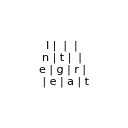

Integreat is a comprehensive Mathematica package for deriving and analyzing time integration methods including

Runge–Kutta (RK) methods

Functions for 30+ method properties

Support for embedded pairs and dense output

Order conditions generated via B-trees

Linear multistep methods (LMMs)

Constructors for Adams methods, BDF, Nyström methods, and other popular families

Functions for 10+ method properties

General linear methods (GLMs)

Functions for 15+ method properties

Support for casting RK methods and LMMs as GLMs

Order conditions for high stage order methods

Trees for Taylor series analysis

B-trees

N-trees for partitioned ODEs

Arbitrary-index DAE-trees

## Documentation

View the online documentation

For catalogs of functions provided by Integreat and links to function documentation, see the guide pages:

Runge–Kutta Methods

Linear Multistep Methods

General Linear Methods

The tech notes provide some mathematical background, example code, and discussions about the package:

Runge–Kutta Methods

Linear Multistep Methods

General Linear Methods

## Examples

Compute properties of a Runge–Kutta method:

0 | 0 | 0 | 0
1/2 | 5/24 | 1/3 | -1/24
1 | 1/6 | 2/3 | 1/6
 | 1/6 | 2/3 | 1/6

{{0,0,0},{5/24,1/3,-1/24},{1/6,2/3,1/6}}

{θ-(3 θ^2)/2+(2 θ^3)/3,2 θ^2-(4 θ^3)/3,-θ^2/2+(2 θ^3)/3}

4

True

0

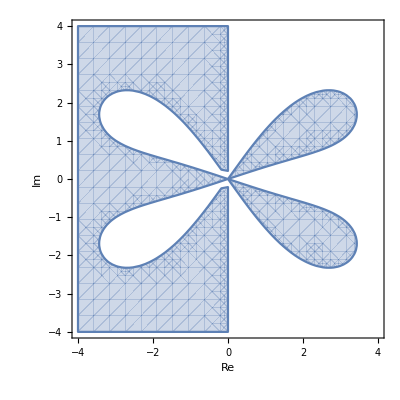

```mathematica
<<Integreat`RK`
rk=RKCollocation[{0,1/2,1}] 
RKA[rk] 
RKDenseOutput[rk]
RKOrder[rk] 
RKAStable[rk]
RKAbsoluteMonotonicityRadius[rk]
RKOrderStarPlot[rk]
```

Derive the second order Adams–Bashforth method:

```mathematica
<<Integreat`LMM`
lmm=LMM[{0,Subscript[a, 1],1},{Subscript[b, 0],Subscript[b, 1],0}] 
oc=LMMOrderConditions[lmm,2] 
sols=Solve[oc==0] 
lmm=lmm/. First[sols]
```

y_(2+n)+y_(1+n) a_1==h (f_n b_0+f_(1+n) b_1)

{(1+a_1)/(b_0+b_1),(2+a_1-b_0-b_1)/(b_0+b_1),(2+a_1/2-b_1)/(b_0+b_1)}

{{a_1→-1,b_0→-1/2,b_1→3/2}}

-y_(1+n)+y_(2+n)==h (-f_n/2+(3 f_(1+n))/2)

## Installation

Installing or upgrading Integreat is as simple as running

```mathematica
PacletInstall["https://github.com/ComputationalScienceLaboratory/Integreat/releases/latest/download/Integreat.paclet"]
```

Once installed, Integreat subpackages can be loaded with

```mathematica
<<Integreat`RK`
<<Integreat`LMM`
<<Integreat`GLM`
```

Integreat can be uninstalled using

```mathematica
PacletUninstall["Integreat"]
```

Related Guides

Integreat Package

Runge–Kutta Methods

Linear Multistep Methods

General Linear Methods

Related Tech Notes

Runge–Kutta Methods

Linear Multistep Method

General Linear Methods

## Metadata

### Categorization

Tech Note

Integreat

Integreat`

Integreat/tutorial/IntegreatPackage

### Keywords